# Condutores Equivalentes

Antonio Carlos Siqueira de Lima
Outubro 2020

Emprego das equipotenciais para comparação da representação expressa dos condutores e empregando RMG

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/acsl/Dropbox/UFRJ/cursos/Transmissão-2020/arquivos_MMA_EE457

## Campos devidos a multi-polos

```mathematica
cargaUni[x_,y_,q_]={{RGBColor[1,1,0],AbsolutePointSize[20],Point[{x,y}]},Text[q,{x,y}]};
```

```mathematica
Multipole[n_]:=∑_(i=1)^n 1/(√((x-Cos[(2 π i)/n+π/4])^2+(y-Sin[(2 π i)/n+π/4])^2))
```

```mathematica
polos[n_]:=Table[ {cargaUni[Cos[(2 π i)/n+π/4],Sin[(2 π i)/n+π/4],"+q"]},{i,1,n}];
```

```mathematica
o1=ContourPlot[Evaluate[Multipole[4]],{x,-2,2},{y,-2,2},PlotPoints->40,Contours->30,ColorFunction->(RGBColor[#,1-#,0.6]&),Epilog-> polos[4]]
```

-Graphics-

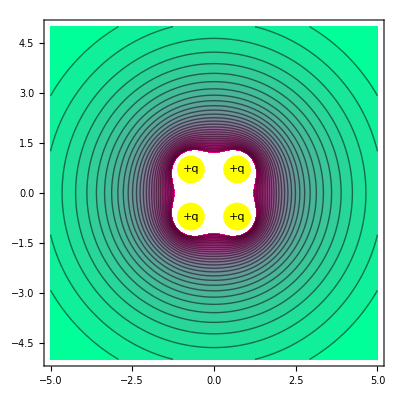

```mathematica
o2=ContourPlot[Evaluate[Multipole[4]],{x,-5,5},{y,-5,5},PlotPoints->40,Contours->30,ColorFunction->(RGBColor[#,1-#,0.6]&),Epilog-> polos[4]]
```

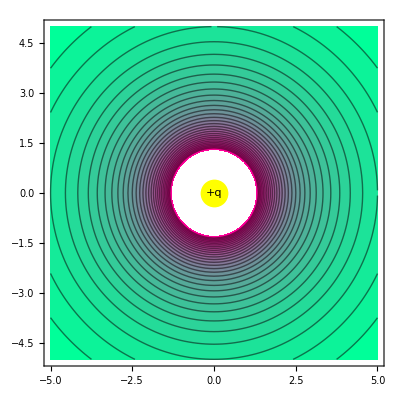

```mathematica
o3= ContourPlot[1/(√((x-0.001)^2+(y-0.001)^2)),{x,-5,5},{y,-5,5},PlotPoints->40,Contours->30,ColorFunction->(RGBColor[#,1-#,0.6]&),Epilog->cargaUni[ 0,0,"+q"]]
```

```mathematica
{o2,o3}
```

{-Graphics-,-Graphics-}